## Collision model dynamics

```mathematica
(*Parameters*)
```

```mathematica
θ =0.1;
ϕ = 1.6;
n=1000;
```

```mathematica
(*Define basis*)
ket0 = {{1},{0}};
ket1 = {{0},{1}};
```

```mathematica
(* Define initial system state*)
```

```mathematica
ψ0 = (ket0+ket1)/Sqrt[2];
ρ0 = ψ0.Transpose[ψ0]
```

{{1/2,1/2},{1/2,1/2}}

```mathematica
(* Define Environment state*)
```

```mathematica
η0 = {{0.4,0},{0,0.6}};
```

```mathematica
(*Define PSWAP operation*)
S =1/2*(KroneckerProduct[PauliMatrix[0],PauliMatrix[0]]+KroneckerProduct[PauliMatrix[1],PauliMatrix[1]]+KroneckerProduct[PauliMatrix[2],PauliMatrix[2]]+KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]);
```

```mathematica
(*Define unitary operator for PSWAP*)
```

```mathematica
U1 = Cos[θ]*KroneckerProduct[PauliMatrix[0],PauliMatrix[0]]+I*Sin[θ]*S;
```

```mathematica
U2 = Cos[ϕ]*KroneckerProduct[PauliMatrix[0],PauliMatrix[0]]+I*Sin[ϕ]*S;
```

```mathematica
(*Define fidelity*)
```

```mathematica
fidelity[ρ_,σ_]:=Module[{sqrtRho,innerProduct},sqrtRho=MatrixPower[ρ,1/2];
innerProduct=sqrtRho.σ.sqrtRho;
Abs[Tr[MatrixPower[innerProduct,1/2]]]^2];
```

```mathematica
(*Initialize the density matrix array*)
```

# Markovian

```mathematica
ρ=ConstantArray[0,{n,2,2}]; 
fidel={}; 
ρ[[1]] =ρ0;
Do[
ρ[[i]]=ResourceFunction["MatrixPartialTrace"][U1.KroneckerProduct[ρ[[i-1]],η0].ConjugateTranspose[U1],{2},2];
AppendTo[fidel,fidelity[η0,ρ[[i]]]];
,{i,2,n}]
```

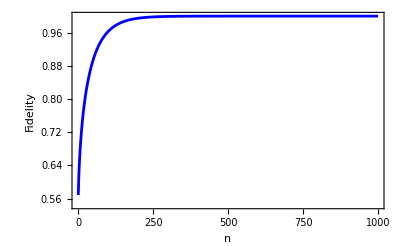

```mathematica
ListLinePlot[fidel,PlotRange->Full,PlotStyle->Blue,LabelStyle->Directive[Black,Bold,{8,GrayLevel[0.1]}],Frame->True,FrameTicks->True,FrameTicksStyle->Black,FrameLabel->{"n","Fidelity" },RotateLabel->True]
```

# Non Markovain case

```mathematica
ClearAll[fnms1]
```

```mathematica
fnms1=ConstantArray[0,n];
```

```mathematica
fnms1[[1]]=fidelity[ρ0, η0];
rho=KroneckerProduct[ρ0, η0];

For[i=2,i<=n,i++,rhoSPrime=ResourceFunction["MatrixPartialTrace"][U1.rho.ConjugateTranspose[U1],{2},2];
rhoBPrime=ResourceFunction["MatrixPartialTrace"][U1.rho.ConjugateTranspose[U1],{1},2];
sigma=KroneckerProduct[rhoBPrime,η0];
rhoBPrime=ResourceFunction["MatrixPartialTrace"][U2.sigma.ConjugateTranspose[U2],{1},2];
fnms1[[i]]=fidelity[rhoSPrime,η0];
rhoBPrime=Round[rhoBPrime,0.000001];
rho=KroneckerProduct[rhoSPrime,rhoBPrime];
]
```

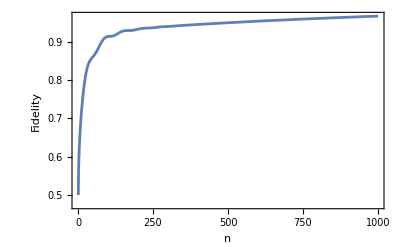

```mathematica
ListLinePlot[{fnms1},PlotRange->Full,LabelStyle->Directive[Black,Bold,{8,GrayLevel[0.1]}],Frame->True,FrameTicks->True,FrameTicksStyle->Black,FrameLabel->{"n","Fidelity" },RotateLabel->True]
```

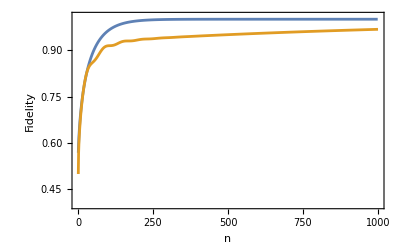

```mathematica
ListLinePlot[{fidel,fnms1},PlotRange->{0.4,1.01},LabelStyle->Directive[Black,Bold,{8,GrayLevel[0.1]}],Frame->True,FrameTicks->True,FrameTicksStyle->Black,FrameLabel->{"n","Fidelity" },RotateLabel->True]
```